#### FindSymGps should be run first. This file gives some embellishments.

```mathematica
Theta[{x_,y_,z_}]:=ArcTan[x,y]; 
(* Theta[{0,0,1}]=Theta[1.{0,0,1}]=0.999; *)
Theta[{0,0,1}]=0;  (* CHANGED FEB 3, 2024 *)
Phi[v_]:=Angle[v,{0,0,1}];
TPxyz0to2pi[v_]:={Mod[Theta[v],2π],Phi[v]};
```

```mathematica
BadSeeds[Tmat_,Σ_,nRuns_]:=Select[Range[0,nRuns-1],nminimize[Tmat,Σ,#][[1]]>.001Degree+nminimize[Tmat,Σ,BestSeed[Tmat,Σ,nRuns]][[1]]&];
SecondaryMinima[Tmat_,Σ_,nRuns_]:=(Clear[θ,ϕ];
{θ,ϕ}/.nminimize[Tmat,Σ,#][[2]]&/@BadSeeds[Tmat,Σ,nRuns]);
```

#### A contour plot for optional use when Σ = MONO or Σ = XISO, and when the minimum for two runs disagree. Note the contours are Automatic, not determined by us.

```mathematica
colorfunction[XISO]=Automatic;
colorfunction[MONO]="TemperatureMap";
```

#### Only for Σ = MONO and Σ = XISO:

```mathematica
Clear[ContourPlotRectangle];
ContourPlotRectangle[Tmat_,Σ_]:=ContourPlotRectangle[Tmat,Σ]=ContourPlot[Alpha[Tmat,{θ,ϕ},Σ]/Degree,{θ,0,2π},{ϕ,0,π},PlotLegends->Automatic,ColorFunction->colorfunction[Σ],
FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic];
```

```mathematica
PrintContourPlotRectangle[Tmat_,Σ_,nRuns_]:=(Print["The contour plot below is of ",Style[SequenceForm[SubsuperscriptBox["α ",Σ,"T"]//DisplayForm,"(θ, ϕ)"],14,Bold], "(Eqs 22 of TT2024)"];
Print["The point (θ_0,ϕ_0) (green) should look like a correct GLOBAL minimum. Any ",If[MemberQ[{MONO},Σ],"black","yellow"]," points should be secondary minima."];
Print["Uniqueness (or not) of the closest ",Σ," map is usually obvious from the contour plot."];
Print[Show[{ContourPlotRectangle[Tmat,Σ],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[Tmat,Σ].{0,0,1}]]},
                                                        {If[MemberQ[{MONO},Σ],Black,Yellow],Point/@SecondaryMinima[Tmat,Σ,nRuns]}}]},
FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]])
```

#### MinimizationFacts is already defined. Here are custom versions for Σ = ISO and Σ =TRIV.

#### For Σ = ISO

```mathematica
λofTmatISO[TmatISO_]:=Simplify[(TmatISO[[6,6]]-TmatISO[[1,1]])/3];
μofTmatISO[TmatISO_]:=Simplify[TmatISO[[1,1]]/2];
κofTmatISO[TmatISO_]:=Simplify[λofTmatISO[TmatISO]+2/3 μofTmatISO[TmatISO]];
Poisson[λ_,μ_]:=λ/(2(λ+μ)) ;
PoissonOfTmatISO[TmatISO_]:=Simplify[Poisson[λofTmatISO[TmatISO],μofTmatISO[TmatISO]]];
```

```mathematica
MinimizationFacts[Tmat_,ISO,nRuns_]:=(
Print["𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ",Style["⟶" ,Bold,14]," d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant."];

Print[textDT[ISO]," = d(T, 𝒯_ISO) = ",dT[Tmat,ISO],"   (Distance from T to 𝒯_ISO)"];  (* dT *)

If[βT[Tmat,ISO]>0,Print["β_ISO^T = ",MyRound[βTinitial[Tmat,ISO],3]," = ",(MyRound[βTinitial[Tmat,ISO]/Degree,2])^o," (Angle between T and 𝒯_ISO)"]]; (* BETA, initial *)

If[βT[Tmat,ISO]==0,
If[βTinitial[Tmat,ISO]==0,
Print["β_ISO^(□T) = 0, (Angle between T and 𝒯_ISO)"]];
If[βTinitial[Tmat,ISO]>0,
Print["β_ISO^(□T) = ",βT[Tmat,ISO]," (Angle between T and 𝒯_ISO. The initial β_ISO^T = ", MyRound[βTinitial[Tmat,ISO],3]," is here chopped to zero, since the chop threshold is set at ",(ChopT/Degree)^o,")"]];  (* BETA, chopped *)
Print["Since β_ISO^(□T) = 0, then T is assigned symmetry ISO."];];

If[βT[Tmat,ISO]>0,   (* closest ISO elastic map *)
Print["P(T,𝒱_ISO(I)) = ",
MatrixForm[1.ProjToVSigOfU[Tmat,id,ISO]],"  (The closest elastic map to T having symmetry ISO)"]];

If[βT[Tmat,ISO]>0 ,        (* Lame parameters and Poisson *)
Print["Lamé parameters for P(T,𝒱_ISO(I))",
" are λ = ",                       λofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],
" and μ = ",                       μofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],
", bulk modulus κ = ",κofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],
", Poisson ratio = ",PoissonOfTmatISO[ProjToVSigOfU[Tmat,id,ISO]]]];
If[βT[Tmat,ISO]==0 , 
Print["Lamé parameters for T are λ = ",λofTmatISO[Tmat],
                                                           " and μ = ",μofTmatISO[Tmat],
                                    ", bulk modulus κ = ",κofTmatISO[Tmat],
                                    ", Poisson ratio = ", PoissonOfTmatISO[Tmat]]];
Print[" "];)
```

#### For TRIV

```mathematica
MinimizationFacts[Tmat_,TRIV,nRunsDum_]:=(
(*Print["The reference group ",Style[Subscript[𝕌, TRIV],14]," is {I}, so ",ScriptV[TRIV,"U"]," = {T : 𝒮_T ⊃ U 𝕌_TRIV U^T} = {T : 𝒮_T ⊃ {I}} = ",Style["𝒯",Bold]," for all U ∈ ",Style[𝕌,13]];*)
Print[                    ScriptT[TRIV]," = 𝒯"];
Print["d_TRIV^T = d(T, 𝒯) = 0 for all elastic maps T"];
Print["β_TRIV^T = ",Style[∠,18],"(T, 𝒯) = 0           '' "];
Print[" "];)
```

## Enter Tmat.

#### Use TmatDemo or change Tmat to suit yourself.

```mathematica
(*MatrixForm[Simplify[16MatrixUbar[XRot[45Degree]].DiagonalMatrix[{1,1,2,3,4,5}].Transpose[MatrixUbar[XRot[45Degree]]]]]*)
```

```mathematica
TmatDemo=({{60, 0, 0, -6, 2 √3, 0}, {0, 24, 8, 0, 0, 0}, {0, 8, 24, 0, 0, 0}, {-6, 0, 0, 43, -9 √3, 0}, {2 √3, 0, 0, -9 √3, 25, 0}, {0, 0, 0, 0, 0, 80}});
MatrixNote[TmatDemo]="Tmat is Demo";
```

```mathematica
Tmat=TmatDemo;
```

#### Note the extraordinary failure in the fourth run, if Tmat = TmatDemo.

```mathematica
Tmat=TmatDemo;
MatrixNote[Tmat]
Σ=XISO;
nRuns=5;
ColumnForm[Table[nminimize[Tmat,Σ,nSeed],{nSeed,0,nRuns-1}]]
```

Tmat is Demo

{11.3137,{θ→1.5708,σ→-1.27838,ϕ→2.35619}}
{11.3137,{θ→1.5708,σ→-2.8925,ϕ→2.35619}}
{11.3137,{θ→1.5708,σ→0.350815,ϕ→2.35619}}
{34.5254,{θ→1.5708,σ→2.75709,ϕ→0.785398}}
{11.3137,{θ→1.5708,σ→-0.236,ϕ→2.35619}}

```mathematica
Tmat=TmatDemo;
Σ=TRIV;
nRuns=2;
MinimizationFacts[Tmat,Σ,nRuns];
```

𝒯_TRIV = 𝒯

d_TRIV^T = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯) = 0           ''

```mathematica
Tmat=TmatDemo;
Σ=ISO;
nRuns=2;
MinimizationFacts[Tmat,Σ,nRuns];
```

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 41.7229   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.356 = 20.39^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (35.2 | 0. | 0. | 0. | 0. | 0.
0. | 35.2 | 0. | 0. | 0. | 0.
0. | 0. | 35.2 | 0. | 0. | 0.
0. | 0. | 0. | 35.2 | 0. | 0.
0. | 0. | 0. | 0. | 35.2 | 0.
0. | 0. | 0. | 0. | 0. | 80.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 224/15 and μ = 88/5, bulk modulus κ = 80/3, Poisson ratio = 14/61

#### An example with PrintContourPlotRectangle:

Tmat is Demo,  Σ = MONO

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_MONO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 3.94161×10^-11 |   6.324973×10^-13 |  -2.527280 |   1.570796
1 | 1.40781×10^-12 |   1.207938×10^-15 |  -0.557934 |   1.570796
2 | 3.17999×10^-7 |   0.615480 |  -2.889288 |   1.047198
3 | 1.86624×10^-8 |   4.712389 |  -0.533550 |   2.356194
4 | 5.03074×10^-12 |   3.723690×10^-14 |   2.279481 |   1.570796

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {6.32497×10^-13,-2.52728,1.5708} = {0.^∘,-144.8^∘,90.^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0 | 0 | 1.
-0.576397 | -0.81717 | 0
0.81717 | -0.576397 | 0)  (One of at least ∞ MONO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

d_MONO^T = d(T, P(T,𝒱_MONO(U_0))) = 3.94×10^-11 (Distance between T and 𝒯_MONO)

β_MONO^T = sin^-1(d_MONO^T/|T|) = 0 (Angle between T and 𝒯_MONO. The initial β_MONO^T = 3.29×10^-13 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_MONO^T = 0, T is assigned symmetry at least MONO.

𝒱_MONO(U_0) contains T

T_MONO = [OverBar[U_0]]^T[T][OverBar[U_0]] = (31.5362 | -2.68426 | 0 | 0 | 0 | 0
-2.68426 | 16.4638 | 0 | 0 | 0 | 0
0 | 0 | 20.9536 | -13.9076 | 2.32464 | 0
0 | 0 | -13.9076 | 55.0464 | -6.52656 | 0
0 | 0 | 2.32464 | -6.52656 | 52. | 0
0 | 0 | 0 | 0 | 0 | 80.)  (Should be a MONO ref matrix for T. If not, consider decreasing ChopT.)

Thus U_0^T will reorient the material so that its symmetry group contains 𝕌_MONO

The contour plot below is of α_MONO^T(θ, ϕ)(Eqs 22 of TT2024)

The point (θ_0,ϕ_0) (green) should look like a correct GLOBAL minimum. Any black points should be secondary minima.

Uniqueness (or not) of the closest MONO map is usually obvious from the contour plot.

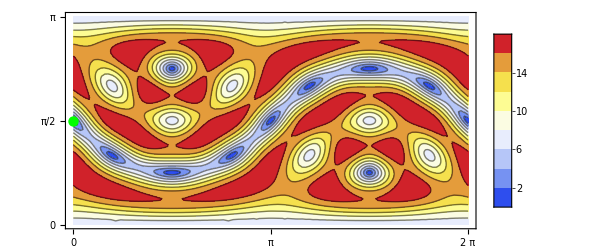

```mathematica
Tmat=TmatDemo;
nRuns=5;
Σ=MONO;
MinimizationFacts[Tmat,Σ,nRuns];
PrintContourPlotRectangle[Tmat,Σ,nRuns]
```

Tmat is Demo,  Σ = XISO

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_XISO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 11.3137 |   1.570796 |  -1.278377 |   2.356194
1 | 11.3137 |   1.570796 |  -2.892500 |   2.356194
2 | 11.3137 |   1.570796 |   0.350815 |   2.356194
3 | 34.5254 |   1.570796 |   2.757092 |   0.785398
4 | 11.3137 |   1.570796 |  -0.236000 |   2.356194

Minimum values for XISO are not the same

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.5708,-1.27838,2.35619} = {90.^∘,-73.2^∘,135.^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.957549 | -0.288269 | 0
-0.203837 | -0.67709 | 0.707107
-0.203837 | -0.67709 | -0.707107)  (One of at least ∞ XISO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

d_XISO^T = d(T, P(T,𝒱_XISO(U_0))) = 11.314 (Distance between T and 𝒯_XISO)

β_XISO^T = sin^-1(d_XISO^T/|T|) = 0.095 = 5.42^o (Angle between T and 𝒯_XISO)

𝒱_XISO(U_0) contains a closest map to T in 𝒯_XISO

P(T, 𝒱_XISO(U_0))= (58. | 0 | 0 | -9. | 5.19615 | 0
0 | 28. | 12. | 0 | 0 | 0
0 | 12. | 28. | 0 | 0 | 0
-9. | 0 | 0 | 38.5 | -12.9904 | 0
5.19615 | 0 | 0 | -12.9904 | 23.5 | 0
0 | 0 | 0 | 0 | 0 | 80.)  (a closest elastic map to T having symmetry at least XISO)

The contour plot below is of α_XISO^T(θ, ϕ)(Eqs 22 of TT2024)

The point (θ_0,ϕ_0) (green) should look like a correct GLOBAL minimum. Any yellow points should be secondary minima.

Uniqueness (or not) of the closest XISO map is usually obvious from the contour plot.

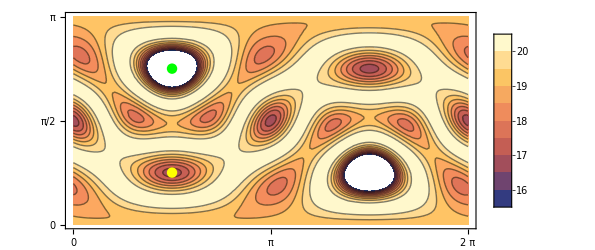

```mathematica
Tmat=TmatDemo;
Σ=XISO;
nRuns=5;
MinimizationFacts[Tmat,Σ,nRuns];
PrintContourPlotRectangle[Tmat,Σ,nRuns]
```

```mathematica
GlobalMinimum[Tmat_,Σ_]:=(Clear[θ,ϕ];{θ,ϕ}/.nminimize[Tmat,Σ,0][[2]]);
```

#### For Σ = MONO or XISO

```mathematica
Clear[PlotAlpha3D];
PlotAlpha3D[Tmat_,Σ_,plotpoints_,nRuns_]:=PlotAlpha3D[Tmat,Σ,plotpoints,nRuns]=Show[{Plot3D[-Alpha[Tmat,{θ,ϕ},Σ]/Degree,{θ,0,2π},{ϕ,0,π},ColorFunction->"TemperatureMap",Mesh->False,PlotPoints->50,PlotLegends->Automatic,PlotRange->All],
Graphics3D[{{PointSize[.0081],Green,
Point[{#[[1]],#[[2]],-Alpha[Tmat,{#[[1]],#[[2]]},Σ]/Degree}]&/@{GlobalMinimum[Tmat,Σ]}},
{PointSize[.0081],Black,
Point[{#[[1]],#[[2]],-Alpha[Tmat,{#[[1]],#[[2]]},Σ]/Degree}]&/@SecondaryMinima[Tmat,Σ,nRuns]},
{Thickness[.002],
Line[{{#[[1]],#[[2]],-Alpha[Tmat,{#[[1]],#[[2]]},Σ]/Degree},
         {#[[1]],        π,-Alpha[Tmat,{#[[1]],#[[2]]},Σ]/Degree}}&/@SecondaryMinima[Tmat,Σ,nRuns]]}}]},BoxRatios->{2π,π,.5π},ImageSize->1000,Ticks->{Range[0,2π,π/2],Range[0,π,π/2],Automatic}]
```

```mathematica
Σ=XISO;
plotpoints=10;
Print[MatrixNote[Tmat],", Σ = ",Σ,", nRuns = ",nRuns,", plotpoints = ",plotpoints];
Print[Green,". Global min"]
Print[Black,". Secondary min, but supposed to be global"]
PlotAlpha3D[Tmat,Σ,plotpoints,nRuns]
```

Tmat is Demo, Σ = XISO, nRuns = 5, plotpoints = 10

RGBColor[0, 1, 0]. Global min

GrayLevel[0]. Secondary min, but supposed to be global

-Graphics3D-